# Wolfram 语言近似求解薄板振动方程

我的研究方向是对微机电压电水听器进行建模，查阅相关文献时往往会遇到这个偏微分方程：

先不管参数 ，让我们关注方程本身，把这个式子当作单纯的“计算对象”。我没能在 Wolfram 的帮助文档里找到“一键式”的数值求解方法，而解析解只能处理固定边圆板、简支边圆板和简支边方板等特殊情况，如果是蜂巢形的水听器单元呢？

面对偏微分方程难解的问题，里兹法的思路大概是：先通过能量分析，把方程问题变成优化问题，再用基函数逼近真实解。在基函数设置时，就可以考虑薄板形状和边界条件的问题，从而得到一个比较通用的程序，利用 Wolfram 语言的内置函数，还可以把这个程序写得更简单。

## 最小作用量，最小物理知识

于我而言，“最小作用量”这套方法是在最小化物理知识的基础上，解决所面临的建模问题。

首先，还是要计算出薄板的动能和势能表达式：

其中  就是众所周知的  这个形式， 则需要参考基尔霍夫薄板理论的应力、应变表达式，并代入线弹性材料应变能的公式里。

补充两点：

积分区域经过尺度变换，所以可以将尺度系数 （不妨理解为“半径”）提到积分之外。

为了简化过程，选取了  的最简形式，这仅对固定边界条件成立，如果是更一般的情况，应该添加一项：

然后，用二者之差代表最小作用量：

“最小”并不意味着“最小”，只是取得极值，或者说对于自变函数  来说，变分 。所以，虽然里兹采用的能量泛函为 ，但这一点区别无关紧要。

另外，最小作用量的被积函数部分，就是拉格朗日量（或拉格朗日密度）。将其代入欧拉-拉格朗日方程后，同样可以得到前面给出的偏微分方程。对我来说，这要比从微元体出发的推导容易太多。

```mathematica
Needs["VariationalMethods`"]
EulerEquations[1/2 ρh D[w[x,y,t],t]^2-1/2 dd (Laplacian[w[x,y,t],{x,y}])^2,w[x,y,t],{x,y,t}]//FullSimplify
```

ρh w^(0,0,2)[x,y,t]+dd (w^(0,4,0)[x,y,t]+2 w^(2,2,0)[x,y,t]+w^(4,0,0)[x,y,t])==0

## 用什么基函数来逼近真实解？

很多文章选取的基函数都很巧妙，既要满足边界条件，又要起到逼近真实解的作用。但我们打算得到比较通用的程序，不能把基函数形式限制在一种特殊场景中。

所以，不妨将基函数写作两项相乘的形式[1]：

边界方程

灰色部分为薄板区域，红色部分为薄板边界：

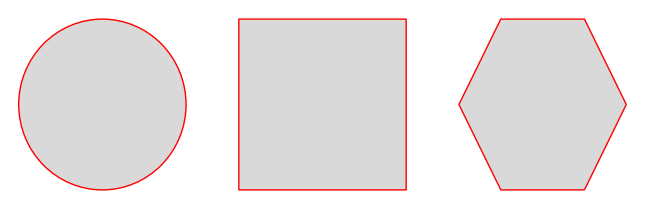

```mathematica
Graphics[{LightGray,#,Red,RegionBoundary@#  }]&/@{Disk[],Rectangle[{-1,-1},{1,1}],RegularPolygon[6]}//GraphicsRow
```

对于圆形薄板来说，其边界方程为：

对于方形薄板来说，其边界方程为：

注意式子里的上标代表该边界的边界条件， 对应于自由边界条件， 对应于简支边界条件， 对应于固定边界条件。

如果是正六边形板，这个边界方程就很难直接写出。可以先写一个函数，能输入各顶点坐标，输出边界方程：

```mathematica
(* 计算两点之间的线方程 *)
lineEquation[{p1_, p2_}, {x_, y_}] := (x - p2[[1]]) (p1[[2]] - p2[[2]]) - (y - p2[[2]]) (p1[[1]] - p2[[1]])

(* 将点列表转换为成对的点 *)
pointsPair[points_List] := Partition[Riffle[#, RotateLeft[#]], 2] &@points

(* 计算多边形的边界 *)
polygonBorder[points_List, {x_, y_}] := Times @@ (lineEquation[#, {x, y}] & /@ pointsPair@points)
```

正六边形的六个顶点即为：

```mathematica
CirclePoints[6]
```

{{1/2,-(√3)/2},{1,0},{1/2,(√3)/2},{-1/2,(√3)/2},{-1,0},{-1/2,-(√3)/2}}

可计算得到边界方程：

```mathematica
polygonBorder[%,{x,y}]
```

(-1/2 √3 (-1/2+x)+1/2 ((√3)/2-y)) ((√3)/2-y) (1/2 √3 (1+x)-y/2) (-1/2 √3 (-1+x)+y/2) ((√3)/2+y) (1/2 √3 (1/2+x)+1/2 ((√3)/2+y))

逼近函数

使用勒让德多项式逼近函数：

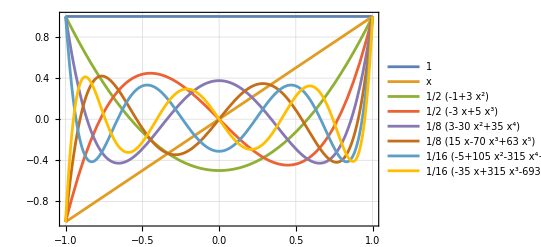

```mathematica
Plot[Evaluate[LegendreP[#,x]&[Range[8]-1]],{x,-1,1},]
```

多项式两两相乘，得到用于函数逼近的二元基函数：

```mathematica
Table[Plot3D[LegendreP[i,x]LegendreP[j,y],{x,-1,1},{y,-1,1},],{i,3},{j,3}]//GraphicsGrid
```

-Graphics-

以固定边界圆板为算例，其基函数形式为：

```mathematica
basicFunctions=Table[LegendreP[i-1,x]LegendreP[j-1,y],{i,4},{j,4}](x^2+y^2-1)^2//Flatten
```

{(-1+x^2+y^2)^2,y (-1+x^2+y^2)^2,1/2 (-1+x^2+y^2)^2 (-1+3 y^2),1/2 (-1+x^2+y^2)^2 (-3 y+5 y^3),x (-1+x^2+y^2)^2,x y (-1+x^2+y^2)^2,1/2 x (-1+x^2+y^2)^2 (-1+3 y^2),1/2 x (-1+x^2+y^2)^2 (-3 y+5 y^3),1/2 (-1+3 x^2) (-1+x^2+y^2)^2,1/2 (-1+3 x^2) y (-1+x^2+y^2)^2,1/4 (-1+3 x^2) (-1+x^2+y^2)^2 (-1+3 y^2),1/4 (-1+3 x^2) (-1+x^2+y^2)^2 (-3 y+5 y^3),1/2 (-3 x+5 x^3) (-1+x^2+y^2)^2,1/2 (-3 x+5 x^3) y (-1+x^2+y^2)^2,1/4 (-3 x+5 x^3) (-1+x^2+y^2)^2 (-1+3 y^2),1/4 (-3 x+5 x^3) (-1+x^2+y^2)^2 (-3 y+5 y^3)}

## 终于变成矩阵问题

为方便计算，先把近似解写成基函数加权求和的形式：

代入动能 、势能  的表达式中，积分部分即为系数矩阵的“二次型”： 和 ，其中  分别称为质量矩阵和刚度矩阵，矩阵元素的表达式为[2]：

继续前面的例子：Wolfram 语言允许我们在区域上进行积分，可计算出刚度矩阵和质量矩阵：

```mathematica
kmatrix=Table[Integrate[Laplacian[basicFunctions[[i]],{x,y}]Laplacian[basicFunctions[[j]],{x,y}],Element[{x,y},Disk[]]],{i,1,16},{j,1,16}];
mmatrix=Table[Integrate[basicFunctions[[i]]basicFunctions[[j]],Element[{x,y},Disk[]]],{i,1,16},{j,1,16}];
```

甚至可以发现，对于圆板来说，两个矩阵的所有元素竟然都有精确解：

```mathematica
kmatrix//MatrixForm
```

((64 π)/3 | 0 | -(20 π)/3 | 0 | 0 | 0 | 0 | 0 | -(20 π)/3 | 0 | (29 π)/15 | 0 | 0 | 0 | 0 | 0
0 | 8 π | 0 | -6 π | 0 | 0 | 0 | 0 | 0 | -(14 π)/5 | 0 | (39 π)/20 | 0 | 0 | 0 | 0
-(20 π)/3 | 0 | (146 π)/15 | 0 | 0 | 0 | 0 | 0 | (38 π)/15 | 0 | -(437 π)/120 | 0 | 0 | 0 | 0 | 0
0 | -6 π | 0 | (40 π)/3 | 0 | 0 | 0 | 0 | 0 | (11 π)/5 | 0 | -(1207 π)/240 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 8 π | 0 | -(14 π)/5 | 0 | 0 | 0 | 0 | 0 | -6 π | 0 | (39 π)/20 | 0
0 | 0 | 0 | 0 | 0 | (8 π)/5 | 0 | -(7 π)/5 | 0 | 0 | 0 | 0 | 0 | -(7 π)/5 | 0 | (159 π)/140
0 | 0 | 0 | 0 | -(14 π)/5 | 0 | 2 π | 0 | 0 | 0 | 0 | 0 | (11 π)/5 | 0 | -(191 π)/112 | 0
0 | 0 | 0 | 0 | 0 | -(7 π)/5 | 0 | (593 π)/280 | 0 | 0 | 0 | 0 | 0 | (49 π)/40 | 0 | -(8577 π)/4480
-(20 π)/3 | 0 | (38 π)/15 | 0 | 0 | 0 | 0 | 0 | (146 π)/15 | 0 | -(437 π)/120 | 0 | 0 | 0 | 0 | 0
0 | -(14 π)/5 | 0 | (11 π)/5 | 0 | 0 | 0 | 0 | 0 | 2 π | 0 | -(191 π)/112 | 0 | 0 | 0 | 0
(29 π)/15 | 0 | -(437 π)/120 | 0 | 0 | 0 | 0 | 0 | -(437 π)/120 | 0 | (9847 π)/3360 | 0 | 0 | 0 | 0 | 0
0 | (39 π)/20 | 0 | -(1207 π)/240 | 0 | 0 | 0 | 0 | 0 | -(191 π)/112 | 0 | (4907 π)/1536 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -6 π | 0 | (11 π)/5 | 0 | 0 | 0 | 0 | 0 | (40 π)/3 | 0 | -(1207 π)/240 | 0
0 | 0 | 0 | 0 | 0 | -(7 π)/5 | 0 | (49 π)/40 | 0 | 0 | 0 | 0 | 0 | (593 π)/280 | 0 | -(8577 π)/4480
0 | 0 | 0 | 0 | (39 π)/20 | 0 | -(191 π)/112 | 0 | 0 | 0 | 0 | 0 | -(1207 π)/240 | 0 | (4907 π)/1536 | 0
0 | 0 | 0 | 0 | 0 | (159 π)/140 | 0 | -(8577 π)/4480 | 0 | 0 | 0 | 0 | 0 | -(8577 π)/4480 | 0 | (467213 π)/161280)

```mathematica
mmatrix//MatrixForm
```

(π/5 | 0 | -(3 π)/40 | 0 | 0 | 0 | 0 | 0 | -(3 π)/40 | 0 | (31 π)/1120 | 0 | 0 | 0 | 0 | 0
0 | π/60 | 0 | -(9 π)/560 | 0 | 0 | 0 | 0 | 0 | -(11 π)/1680 | 0 | (111 π)/17920 | 0 | 0 | 0 | 0
-(3 π)/40 | 0 | (37 π)/1120 | 0 | 0 | 0 | 0 | 0 | (31 π)/1120 | 0 | -(437 π)/35840 | 0 | 0 | 0 | 0 | 0
0 | -(9 π)/560 | 0 | (317 π)/17920 | 0 | 0 | 0 | 0 | 0 | (111 π)/17920 | 0 | -(1453 π)/215040 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | π/60 | 0 | -(11 π)/1680 | 0 | 0 | 0 | 0 | 0 | -(9 π)/560 | 0 | (111 π)/17920 | 0
0 | 0 | 0 | 0 | 0 | π/840 | 0 | -(11 π)/8960 | 0 | 0 | 0 | 0 | 0 | -(11 π)/8960 | 0 | (19 π)/15360
0 | 0 | 0 | 0 | -(11 π)/1680 | 0 | (31 π)/10752 | 0 | 0 | 0 | 0 | 0 | (111 π)/17920 | 0 | -(39 π)/14336 | 0
0 | 0 | 0 | 0 | 0 | -(11 π)/8960 | 0 | (449 π)/322560 | 0 | 0 | 0 | 0 | 0 | (19 π)/15360 | 0 | -(397 π)/286720
-(3 π)/40 | 0 | (31 π)/1120 | 0 | 0 | 0 | 0 | 0 | (37 π)/1120 | 0 | -(437 π)/35840 | 0 | 0 | 0 | 0 | 0
0 | -(11 π)/1680 | 0 | (111 π)/17920 | 0 | 0 | 0 | 0 | 0 | (31 π)/10752 | 0 | -(39 π)/14336 | 0 | 0 | 0 | 0
(31 π)/1120 | 0 | -(437 π)/35840 | 0 | 0 | 0 | 0 | 0 | -(437 π)/35840 | 0 | (771 π)/143360 | 0 | 0 | 0 | 0 | 0
0 | (111 π)/17920 | 0 | -(1453 π)/215040 | 0 | 0 | 0 | 0 | 0 | -(39 π)/14336 | 0 | (1021 π)/344064 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -(9 π)/560 | 0 | (111 π)/17920 | 0 | 0 | 0 | 0 | 0 | (317 π)/17920 | 0 | -(1453 π)/215040 | 0
0 | 0 | 0 | 0 | 0 | -(11 π)/8960 | 0 | (19 π)/15360 | 0 | 0 | 0 | 0 | 0 | (449 π)/322560 | 0 | -(397 π)/286720
0 | 0 | 0 | 0 | (111 π)/17920 | 0 | -(39 π)/14336 | 0 | 0 | 0 | 0 | 0 | -(1453 π)/215040 | 0 | (1021 π)/344064 | 0
0 | 0 | 0 | 0 | 0 | (19 π)/15360 | 0 | -(397 π)/286720 | 0 | 0 | 0 | 0 | 0 | -(397 π)/286720 | 0 | (58301 π)/37847040)

用矩阵热图进行可视化，不难发现这两个矩阵都是对称矩阵，利用这一特性可以减少运算量。

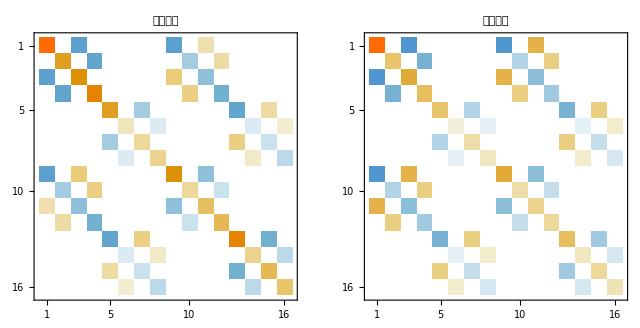

```mathematica
MatrixPlot[#[[1]],PlotLabel->#[[2]]]&/@{{kmatrix,"刚度矩阵"},{mmatrix,"质量矩阵"}}//GraphicsRow
```

通过选取合适的系数，取得作用量的极值，即作用量对向量  求导为零：

化简得到：

```mathematica
{vals,coefs}=Eigensystem[{N@kmatrix,N@mmatrix},-4];
```

把优化问题转化为质量矩阵和刚度矩阵的广义特征值求解问题，将特征向量  与基函数向量  点乘，即得近似解表达式。可将前四个模态的密度图绘制如下：

```mathematica
DensityPlot[#[[2]].basicFunctions,]&/@//GraphicsRow
```

-Graphics-

其中的密度图为模态振型，上面的数字为特征值 ，与以下微分特征方程中的特征值  与半径  的乘积近似相等：

## 程序简化并总结为函数

参考上述分析过程，有以下几点优化空间：

质量矩阵、刚度矩阵均为对称矩阵，可削减计算量：

```mathematica
Table[N@Integrate[Laplacian[basicFunctions[[i]],{x,y}]Laplacian[basicFunctions[[j]],{x,y}],Element[{x,y},Disk[]]],{i,1,16},{j,1,16}];//RepeatedTiming
```

{1.52804,Null}

```mathematica
Table[N@Integrate[Laplacian[basicFunctions[[i]],{x,y}]Laplacian[basicFunctions[[j]],{x,y}],Element[{x,y},Disk[]]],{i,1,16},{j,1,i}];//RepeatedTiming
```

{0.813599,Null}

计算积分时可并行计算，以减少程序耗时：

```mathematica
$ProcessorCount
```

4

```mathematica
ParallelTable[N@Integrate[Laplacian[basicFunctions[[i]],{x,y}]Laplacian[basicFunctions[[j]],{x,y}],Element[{x,y},Disk[]]],{i,1,16},{j,1,i}];//RepeatedTiming
```

{0.355318,Null}

为编写更具一般性的程序，应使用数值积分。对于矩阵中存在的大量零元素，需要设定合适的准确度目标：

```mathematica
ParallelTable[NIntegrate[Laplacian[basicFunctions[[i]],{x,y}]Laplacian[basicFunctions[[j]],{x,y}],Element[{x,y},Disk[]],AccuracyGoal->5],{i,1,16},{j,1,i}];//RepeatedTiming
```

{1.47974,Null}

于是，将优化后的函数整合为一个程序包：

```mathematica
Clear[polygonBorder,lineEquation,pointsPair]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"RitzMethod.wl"}]]
```

```mathematica
?RitzSolver
```

对于上面的固定边界圆板，可以这样调用函数：

```mathematica
cd=RitzSolver[{4,4},{(x^2+y^2-1),Disk[]},{x,y}];
DensityPlot[#[[2]],]&/@()//GraphicsRow
```

-Graphics-

对于简支边界方板，需要多设置两个参数，一个是边界方程的指数，另一个是泊松比：

```mathematica
sr=RitzSolver[{4,4},{(x-1) (x+1) (y-1) (y+1),1,Rectangle[{-1,-1},{1,1}],0.3},{x,y}];
DensityPlot[#[[2]],]&/@()//GraphicsRow
```

-Graphics-

实际上，参考此算例的解析解表达式，可知泊松比并不影响结果：

```mathematica
SSSquare[{m_,n_},{x_,y_}]:={Pi Sqrt[(m/2)^2+(n/2)^2],Sin[Pi m(x+1)/2]Sin[Pi n(y+1)/2]}
```

绘图，并与里兹解作比较：

```mathematica
DensityPlot[#[[2]],{x,-1,1},{y,-1,1},PlotLabel->N@#[[1]]]&/@Flatten[#,1]&@Table[SSSquare[{i,j},{x,y}],{i,2},{j,2}]//GraphicsRow
```

-Graphics-

最后是固定边界正六边形板，也就是我在文章最开始讲的“蜂巢形的水听器单元”：

```mathematica
ch=RitzSolver[{4,4},{polygonBorder[#,{x,y}],2,Polygon@#,1},{x,y}]&@CirclePoints[6];
DensityPlot[#[[2]],]&/@()//GraphicsRow
```

-Graphics-

第一个解看上去有些奇怪，可以绘制出立体图形，只是凹陷而已：

```mathematica
Plot3D[Last@Last@Transpose@ch,Element[{x,y},RegularPolygon@6],]
```

-Graphics3D-

本文处理的方程是齐次的，所以不管解的幅值是多少，都能满足该方程，但为了方便后续处理，一般会对幅值作归一化：

```mathematica
{disk,square,hexagon}=RitzSolver[#,{x,y}]&/@{"Disk","Square","Hexagon"}; (*程序包中预存了固定边界的圆形、方形和正六边形的解*)
Plot3D[#[[1]],Element[{x,y},#[[2]]],]&/@{}//GraphicsRow
```

-Graphics-

为了降低理解难度，文中略去了许多细节。比如一般边界条件的刚度矩阵元素表达式，你可以在程序文件中找到。至于更详细的推导过程，可以参考下面列出的两篇文献，或者自行搜索 "基尔霍夫薄板理论" 的相关内容。

## 参考文献

1.	Zhao, J. (2023). Variable stiffness discrete Ritz method for free vibration analysis of plates in arbitrary geometries. Journal of Sound and Vibration, 553, 117662.

2.	Leissa, A. W. (2005). The historical bases of the Rayleigh and Ritz methods. Journal of Sound and Vibration, 287(4–5), 961–978.